```mathematica
h=1/10;
V=10;
```

```mathematica
x0=-8;
y0=0;
```

```mathematica
bsbe =FindRoot[{h*((1/2)Log[(Cos[bs/2]+Sin[bs/2])/(Cos[bs/2]-Sin[bs/2])]-(1/2)Log[(Cos[be/2]+Sin[be/2])/(Cos[be/2]-Sin[be/2])]+1/Cos[be]*(Sin[bs]/Cos[bs]-Sin[be]/Cos[be])-(Cos[bs/2]*Sin[bs/2])/(1-4*(Cos[bs/2])^2*(Sin[bs/2])^2)+(Cos[be/2]*Sin[be/2])/(1-4*(Cos[be/2])^2*(Sin[be/2])^2))==x0,h*((1/(Cos[bs]) - 1/Cos[be]))==y0},{{bs,-1},{be,1}}, Method->"Secant"]
```

{bs→-1.68453,be→1.68453}

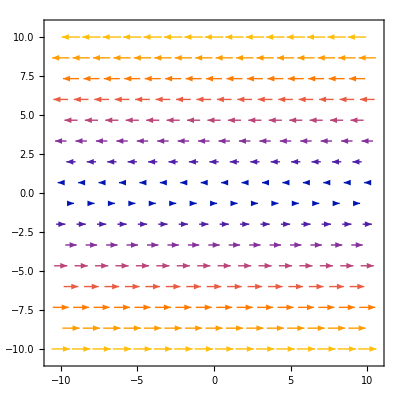

```mathematica
VectorPlot[{-(V/h)*y,0},{x,-10,10},{y,-10,10},VectorScaling->Automatic,VectorSizes->Automatic]
```

```mathematica
ts=0;
tend=Solve[{Tan[bs]-Tan[be]==(V/h)*(ts-te)}/.bsbe,te];
time={t,ts,te/.tend};
eqs={x'[t]==V*Cos[b[t]]-(V/h)*y[t],
y'[t]==V*Sin[b[t]],
b'[t]==(V/h)*(Cos[b[t]])^2};
```

```mathematica
sol=NDSolve[Join[eqs,{x[0]==x0,y[0]==y0,b[0]==bs/.bsbe}],{x[t],y[t],b[t]},{t,0,10}];
```

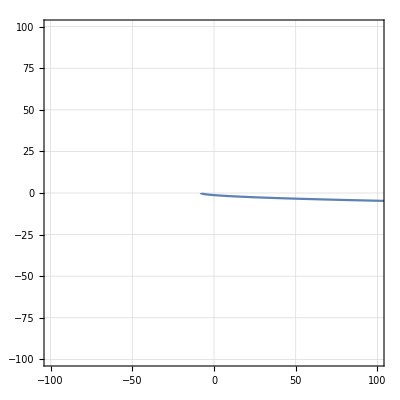

```mathematica
ParametricPlot[{x[t],y[t]}/.sol,{t,0,10},Frame->True,GridLines->Automatic,PlotRange->{{-100,100},{-100,100}}]
```